#### Harmonic Oscillator

```mathematica
HamHO=(-Ec D[#, {ϕ,2}]+EL ϕ^2#&)
```

-Ec ∂_{ϕ,2} #1+EL ϕ^2 #1&

```mathematica
HamHO[ψ[ϕ]]
```

EL ϕ^2 ψ[ϕ]-Ec ψ''[ϕ]

```mathematica
const={Ec->1,EL->1};
```

```mathematica
solHO=NDEigensystem[{HamHO[ψ[ϕ]]/.const,ψ[-10]==ψ[10]},ψ,{ϕ,-10,10},10,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.25}}}]
```

{{1.00001,3.00007,5.00025,7.00063,9.00128,11.0023,13.0037,15.0056,17.0081,19.0112},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

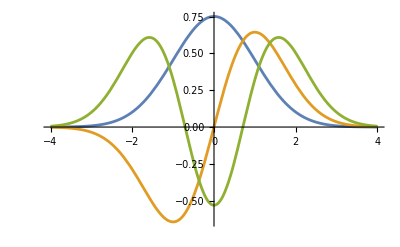

```mathematica
Plot[Evaluate[Table[solHO[[2,j]][ϕ],{j,1,3}]],{ϕ,-4,4}]
```

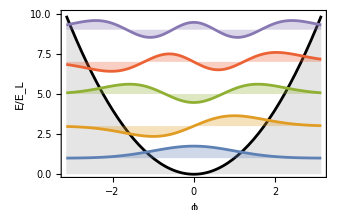

```mathematica
Show[Plot[EL  ϕ^2 /.const,{ϕ,-π,π},PlotStyle->Black,Filling->Bottom,Frame->True,PlotRange->{All,{0,10}},FillingStyle->Opacity[0.1],ImageSize->{12  72/2.54,Automatic},BaseStyle->{FontSize->12},GridLines->{{-2π,-π,0,π,2π},Automatic},FrameLabel->{ϕ,("E")/("E_L")},RotateLabel->False],{#[[1]]+(#[[2]][ϕ])/Exp[I Arg[#[[2]][2]]],#[[1]]}&/@(solHOᵀ)[[1;;5]]//Plot[Evaluate[#[[All,1]]],{ϕ,-π,π},PlotRange->All,Filling->(Thread[Range[Length[#]]->#[[All,2]]]),FillingStyle->{Opacity[0.3]}]&]
```

#### Josephson nonlinear circtuit

```mathematica
HamJJ=(-Ec D[#, {ϕ,2}]-EJ Cos[ϕ]#&)
```

-Ec ∂_{ϕ,2} #1-EJ Cos[ϕ] #1&

```mathematica
HamJJ[ψ[ϕ]]
```

-EJ Cos[ϕ] ψ[ϕ]-Ec ψ''[ϕ]

```mathematica
constJJ={Ec->1,EJ->2};
```

```mathematica
solJJ=NDEigensystem[{HamJJ[ψ[ϕ]]/.constJJ,ψ[-π]==ψ[π]},ψ,{ϕ,-π,π},10,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.25}}}]//Transpose//Sort//Transpose
```

{{-1.07012,0.686756,1.70731,4.1134,4.16283,9.0609,9.06104,16.0506,16.0506,25.0896},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

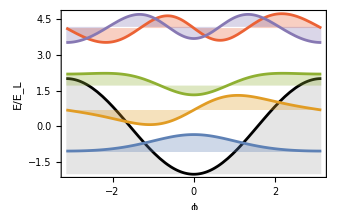

```mathematica
Show[Plot[-EJ Cos[ϕ] /.constJJ,{ϕ,-π,π},PlotStyle->Black,Filling->Bottom,Frame->True,PlotRange->{-2,All},FillingStyle->Opacity[0.1],ImageSize->{12  72/2.54,Automatic},BaseStyle->{FontSize->12},GridLines->{{-2π,-π,0,π,2π},Automatic},FrameLabel->{ϕ,("E")/("E_L")},RotateLabel->False],{#[[1]]+(#[[2]][ϕ])/Exp[I Arg[#[[2]][2]]],#[[1]]}&/@(solJJᵀ)[[1;;5]]//Plot[Evaluate[#[[All,1]]],{ϕ,-π,π},PlotRange->{-2,All},Filling->(Thread[Range[Length[#]]->#[[All,2]]]),FillingStyle->{Opacity[0.3]}]&]
```

```mathematica
RotateLeft[solJJ[[1]]]-solJJ[[1]]
```

{1.75688,1.02056,2.40609,0.0494314,4.89807,0.000134934,6.98958,7.70858×10^-8,9.03894,-26.1597}

```mathematica
constJJ={Ec->1,EJ->20};
```

```mathematica
solJJ=NDEigensystem[{HamJJ[ψ[ϕ]]/.constJJ,ψ[-π]==ψ[π]},ψ,{ϕ,-π,π},10,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.25}}}]//Transpose//Sort//Transpose
```

{{-16.9013,-10.8365,-5.04687,0.443828,5.60127,10.3884,14.5948,18.8323,20.4959,27.2227},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

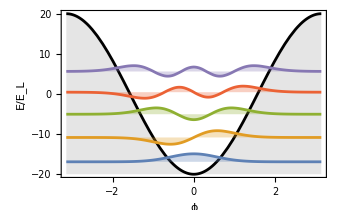

```mathematica
Show[Plot[-EJ Cos[ϕ] /.constJJ,{ϕ,-π,π},PlotStyle->Black,Filling->Bottom,Frame->True,PlotRange->{-20,All},FillingStyle->Opacity[0.1],ImageSize->{12  72/2.54,Automatic},BaseStyle->{FontSize->12},GridLines->{{-2π,-π,0,π,2π},Automatic},FrameLabel->{ϕ,("E")/("E_L")},RotateLabel->False],{#[[1]]+(2#[[2]][ϕ])/Exp[I Arg[#[[2]][2]]],#[[1]]}&/@(solJJᵀ)[[1;;5]]//Plot[Evaluate[#[[All,1]]],{ϕ,-π,π},PlotRange->{-20,All},Filling->(Thread[Range[Length[#]]->#[[All,2]]]),FillingStyle->{Opacity[0.3]}]&]
```

```mathematica
constJJ={Ec->1,EJ->0.2};
```

```mathematica
solJJ=NDEigensystem[{HamJJ[ψ[ϕ]]/.constJJ,ψ[-π]==ψ[π]},ψ,{ϕ,-π,π},10,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.25}}}]//Transpose//Sort//Transpose
```

{{-0.0196622,0.996674,1.01633,4.00163,4.00164,9.00393,9.00393,16.0188,16.0188,25.0691},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

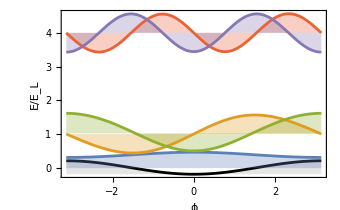

```mathematica
Show[Plot[-EJ Cos[ϕ] /.constJJ,{ϕ,-π,π},PlotStyle->Black,Filling->Bottom,Frame->True,PlotRange->{-0.2,All},FillingStyle->Opacity[0.1],ImageSize->{12  72/2.54,Automatic},BaseStyle->{FontSize->12},GridLines->{{-2π,-π,0,π,2π},Automatic},FrameLabel->{ϕ,("E")/("E_L")},RotateLabel->False],{#[[1]]+(#[[2]][ϕ])/Exp[I Arg[#[[2]][2]]],#[[1]]}&/@(solJJᵀ)[[1;;5]]//Plot[Evaluate[#[[All,1]]],{ϕ,-π,π},PlotRange->{-0.2,All},Filling->(Thread[Range[Length[#]]->#[[All,2]]]),FillingStyle->{Opacity[0.3]}]&]
```